# Incomplete ILU

The plan is to implement this pseudo code 
-Graphics-
https://www.cfd-online.com/Wiki/Incomplete_LU_factorization_-_ILU

## Test Problem

I found a tiny test problem.  I added the identity matrix since the test problem needs to have non zero diagonal elements.

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/chemimp/impcol_b.mtx.gz"];
(* Adding 1 to each diagonal entry *)
Do[A⟦i,i⟧+=1,{i,Length[A]}]
(* Saving a copy of the test matrix *)
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\GitHub\\23-24-Classes\\Spring 2024 Courses\\Lin Alg\\Projects\\ILU0"]
Export["ILU0Test.mtx",A]
```

C:\Users\AllanStruthers\Desktop\GitHub\23-24-Classes\Spring 2024 Courses\Lin Alg\Projects\ILU0

ILU0Test.mtx

```mathematica
A=ExampleData[{"Matrix","494BUS"}];
(* Checking for non-zero diagonal entries *)
Min[Abs[Diagonal[A]]];
(* Computing the Length *)
n=Length[A];
(* Finding locations and values of the non-zero elements *) 
Do[
d=1.0/A⟦r,r⟧;
Do[
A⟦All,r⟧
],
{r,1,n-1}]
```

```mathematica
(* extracting the locations of nonzeros in column c *)
(* Always a diagonal element sub and supper diagonal elements *)
c=456;
nzcol=Flatten[Keys[ArrayRules[A⟦All,c⟧]]⟦1;;-2⟧]
(* in the pseudo code it says i from r+1 to n  *)
```

{297,456,457,458}

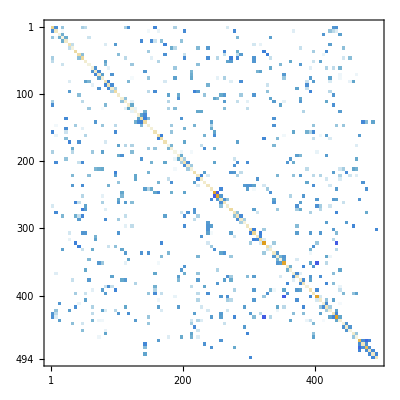

-Graphics-

```mathematica
{LU,p,c}=LUDecomposition[A];
MatrixPlot[A]
MatrixPlot[LU]
```

```mathematica
r1=5;
r2=123;
v1 =A⟦r1,All⟧
v2=A⟦r2,All⟧
v1+v2
```

SparseArray[…]

SparseArray[…]

SparseArray[…]